```mathematica
c1= Circle[{32,20},256]; c2 = Circle[{32,44},256]
```

Circle[{32,44},256]

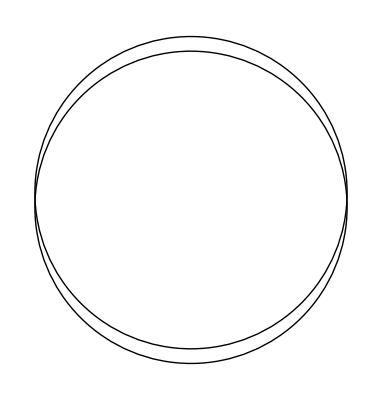

```mathematica
Graphics[{c1,c2}]
```

```mathematica
c3 = Circle[{8,5},16]; c4=Circle[{8,11},16];
```

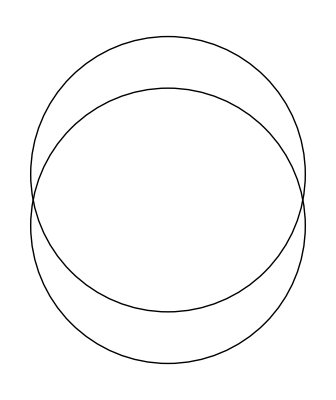

```mathematica
Graphics[{c3,c4}]
```

Using implicit region to calculate overlap of regions:

```mathematica
reg=ImplicitRegion[((x-8)^2+(y-5)^2<16 && (y < 8)) ,{x,y}]
```

ImplicitRegion[(-8+x)^2+(-5+y)^2<16&&y<8,{x,y}]

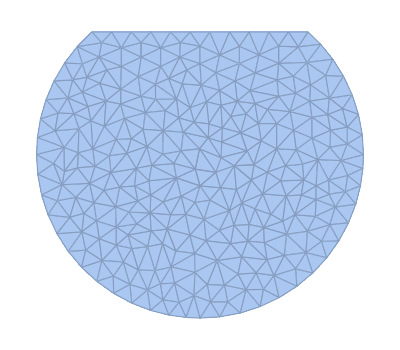

```mathematica
DiscretizeRegion[reg]
```

```mathematica
reg1 = ImplicitRegion[((x-8)^2+(y-11)^2< 16 && (y >8)),{x,y}]
```

ImplicitRegion[(-8+x)^2+(-11+y)^2<16&&y>8,{x,y}]

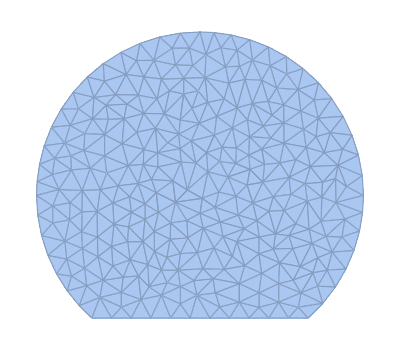

```mathematica
DiscretizeRegion[reg1]
```

```mathematica
reg2 = ImplicitRegion[((x-32)^2+(y-20)^2< 256 && y < 32) &&
((x-32)^2+(y-44)^2<270 && y ≥ 32),{x,y}]
```

ImplicitRegion[(-32+x)^2+(-20+y)^2<256&&y<32&&(-32+x)^2+(-44+y)^2<270&&y≥32,{x,y}]

```mathematica
DiscretizeRegion[reg2]
```

DiscretizeRegion[ImplicitRegion[(-32+x)^2+(-20+y)^2<256&&y<32&&(-32+x)^2+(-44+y)^2<270&&y≥32,{x,y}]]

```mathematica
reg3=ImplicitRegion[((x-32)^2+(y-20)^2< 256 && y < 32),{x,y}];
```

```mathematica
reg4=ImplicitRegion[((x-32)^2+(y-44)^2<270 && y ≥ 32),{x,y}];
```

```mathematica
g1 = DiscretizeRegion[reg3];
```

```mathematica
g2 = DiscretizeRegion[reg4];
```

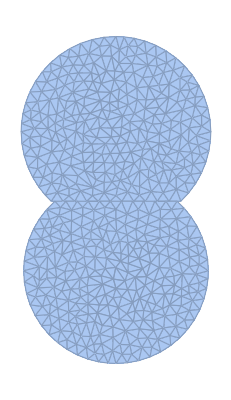

```mathematica
Show[{g1,g2}]
```